# Practical 1 Bisection Method

### Question 1:

1th iteration value is : -1/2

2th iteration value is : -1/4

3th iteration value is : -1/8

4th iteration value is : -1/16

5th iteration value is : -1/32

6th iteration value is : -1/64

7th iteration value is : -1/128

8th iteration value is : -1/256

9th iteration value is : -1/512

10th iteration value is : -1/1024

11th iteration value is : -1/2048

12th iteration value is : -1/4096

13th iteration value is : -1/8192

Return[-1/16384]

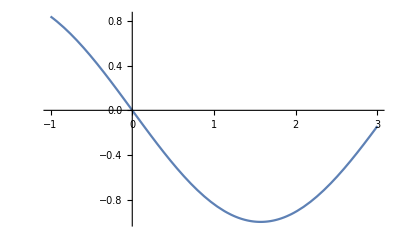

```mathematica
x0 = -1;
 x1 = 0;
Nmax = 20;
eps = 0.0001;
 f[x_] :=-Sin[x];
 If[N[f[x0]*f[x1]]>0,
 Print["Your values do not satisfy the IVP so change the value."],
 For[i=1,i≤ Nmax,i++,m=(x0+x1)/2;
 If[Abs[(x1-x0)/2]<eps,Return[m],
 Print[i,"th iteration value is : ",m];
 If[f[m]*f[x1]>0,x1=m,x0=m]]];
 Print["Root is:",m]]
   Plot[f[x],{x,-1,3}]
```

#### Question 2:

1th iteration value is : -2

2th iteration value is : -3/2

3th iteration value is : -5/4

4th iteration value is : -9/8

5th iteration value is : -19/16

6th iteration value is : -39/32

7th iteration value is : -77/64

8th iteration value is : -153/128

9th iteration value is : -307/256

10th iteration value is : -615/512

11th iteration value is : -1231/1024

12th iteration value is : -2461/2048

13th iteration value is : -4921/4096

14th iteration value is : -9841/8192

Return[-19683/16384]

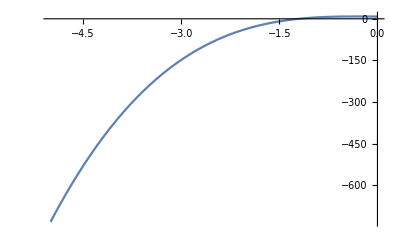

```mathematica
x0 = -3;
 x1 = -1;
Nmax = 20;
eps = 0.0001;
 f[x_] := 6x^3-2x+8;
 If[N[f[x0]*f[x1]]>0,
 Print["Your values do not satisfy the IVP so change the value."],
 For[i=1,i≤ Nmax,i++,m=(x0+x1)/2;
 If[Abs[(x1-x0)/2]<eps,Return[m],
 Print[i,"th iteration value is : ",m];
 If[f[m]*f[x1]>0,x1=m,x0=m]]];
 Print["Root is:",m]]
   Plot[f[x],{x,-5,0}]
```

#### Question 3:

1th iteration value is : -2

2th iteration value is : -3/2

3th iteration value is : -7/4

4th iteration value is : -15/8

5th iteration value is : -29/16

6th iteration value is : -59/32

7th iteration value is : -119/64

8th iteration value is : -239/128

9th iteration value is : -477/256

10th iteration value is : -955/512

11th iteration value is : -1909/1024

12th iteration value is : -3817/2048

13th iteration value is : -7635/4096

14th iteration value is : -15269/8192

Return[-30539/16384]

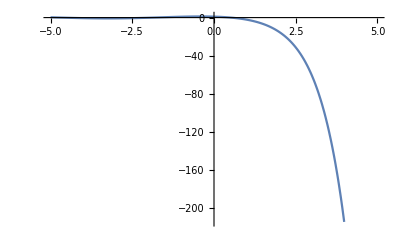

```mathematica
x0 = -3;
 x1 = -1;
Nmax = 20;
eps = 0.0001;
 f[x_] := Cos[x] - x * Exp[x];
 If[N[f[x0]*f[x1]]>0,
 Print["Your values do not satisfy the IVP so change the value."],
 For[i=1,i≤ Nmax,i++,m=(x0+x1)/2;
 If[Abs[(x1-x0)/2]<eps,Return[m],
 Print[i,"th iteration value is : ",m];
 If[f[m]*f[x1]>0,x1=m,x0=m]]];
 Print["Root is:",m]]
Plot[f[x],{x,-5,5}]
```

#### Question 4:

1th iteration value is : 1.75

2th iteration value is : 1.625

3th iteration value is : 1.5625

4th iteration value is : 1.59375

5th iteration value is : 1.60938

6th iteration value is : 1.61719

7th iteration value is : 1.62109

8th iteration value is : 1.61914

9th iteration value is : 1.61816

10th iteration value is : 1.61768

11th iteration value is : 1.61792

12th iteration value is : 1.61804

Return[1.61798]

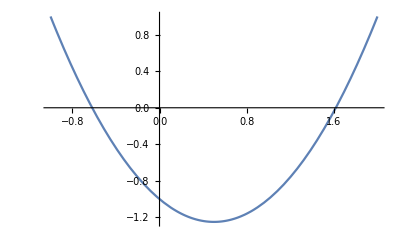

```mathematica
x0 = 1.5;
 x1 = 2;
Nmax = 20;
eps = 0.0001;
 f[x_] := x^2-x-1;
 If[N[f[x0]*f[x1]]>0,
 Print["Your values do not satisfy the IVP so change the value."],
 For[i=1,i≤ Nmax,i++,m=(x0+x1)/2;
 If[Abs[(x1-x0)/2]<eps,Return[m],
 Print[i,"th iteration value is : ",m];
 If[f[m]*f[x1]>0,x1=m,x0=m]]];
 Print["Root is:",m]]
Plot[f[x],{x,-1,2}]
```

# Practical 2 Secant Method

```mathematica
ClearAll;
Clear[x];
```

```mathematica
secant[f_,a0_,b0_,n_]:=Module[{},a=N[a0];
b=N[b0];
If[f[a]*f[b]>0,Print[" Secant method cannot be applied"];
Return[]];
i=1;
While[i<=n,p=N[b-((b-a)*f[b]/(f[b]-f[a]))];
Print[i,"          ",a,"            ",b];
i++;
a=b;
b=p];
Print[" Root = ",p]]
```

#### Question 1

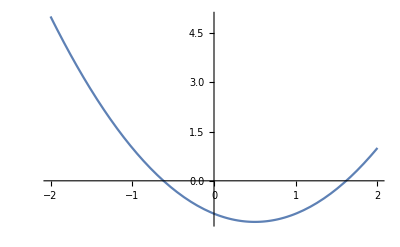

```mathematica
f[x_] := x^2-x-1;
Plot[f[x], {x,-2,2}]
```

```mathematica
secant[f,-1,0,5]
```

1          -1.            0.

2          0.            -0.5

3          -0.5            -0.666667

4          -0.666667            -0.615385

5          -0.615385            -0.617978

Root = -0.618034

```mathematica
secant[f,1,2,6]
```

1          1.            2.

2          2.            1.5

3          1.5            1.6

4          1.6            1.61905

5          1.61905            1.61803

6          1.61803            1.61803

Root = 1.61803

#### Question 2

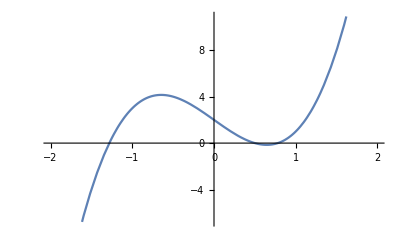

```mathematica
f[x_] := 4x^3-5x+2;
Plot[f[x], {x,-2,2}]
```

```mathematica
secant[f,-2,-1,5]
```

1          -2.            -1.

2          -1.            -1.13043

3          -1.13043            -1.34749

4          -1.34749            -1.26958

5          -1.26958            -1.28003

Root = -1.28079

#### Question 3

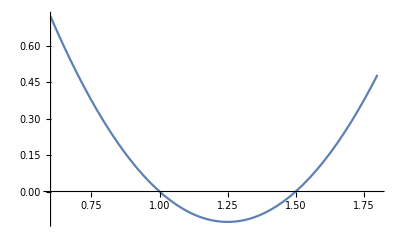

```mathematica
f[x_] := 2x^2-5x+3;
Plot[f[x], {x,0.6,1.8}]
```

```mathematica
secant[f,0.7,1.2,4]
```

1          0.7            1.2

2          1.2            1.1

3          1.1            0.9

4          0.9            1.02

Root = 1.00345

```mathematica
secant[f,1.3,1.7,6]
```

1          1.3            1.7

2          1.7            1.42

3          1.42            1.47419

4          1.47419            1.50524

5          1.50524            1.49972

6          1.49972            1.5

Root = 1.5

#### Question 4

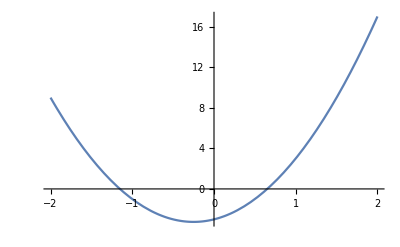

```mathematica
f[x_] := 4x^2+2x-3;
Plot[f[x], {x,-2,2}]
```

```mathematica
secant[f,-2,-1,5]
```

1          -2.            -1.

2          -1.            -1.1

3          -1.1            -1.15625

4          -1.15625            -1.15125

5          -1.15125            -1.15139

Root = -1.15139

```mathematica
secant[f,0,1,4]
```

1          0.            1.

2          1.            0.5

3          0.5            0.625

4          0.625            0.653846

Root = 0.651351

# Regula-Falsi Method

```mathematica
ClearAll;
Clear[x];
```

```mathematica
regulafalsi[a0_,b0_,n_]:=Module[{},s=N[a0];
t=N[b0];
u=(s*f[t]-t*f[s])/(f[t]-f[s]);
k=0;
While[k<1,If[Sign[f[t]]==Sign[f[u]],u=t,s=u];
u=(s*f[t]-t*f[s])/(f[t]-f[s]);
k=k+n];
Print["u = ",NumberForm[u,16]];
Print["f[u] = ",NumberForm[f[u],16]];]
```

#### Question 1

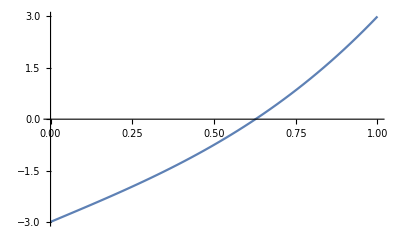

```mathematica
f[x_]:= 2x^3+4x-3;
Plot[f[x],{x,0,1}]
```

```mathematica
regulafalsi[0.4,0.8,20]
```

u = 0.6245265492918916

f[u] = -0.01472136255841683

#### Question 2

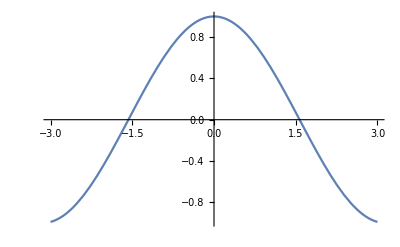

```mathematica
f[x_]:=Cos[x];
Plot[f[x], {x,-3,3}]
```

```mathematica
regulafalsi[-2,-1,15]
```

u = -1.564904375891578

f[u] = 0.005891916813448232

```mathematica
regulafalsi[1,2,20]
```

u = 1.570978574535018

f[u] = -0.0001822477391127237

#### Question 3

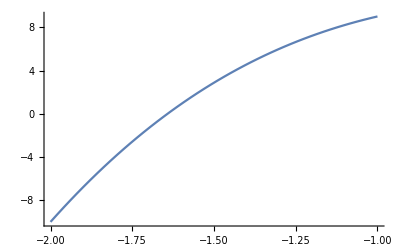

```mathematica
f[x_]:=3x^3-2x+10;
Plot[f[x],{x,-2,-1}]
```

```mathematica
regulafalsi[-1.7,-1.6,20]
```

u = -1.640515326521546

f[u] = 0.03572053303477318

#### Question 4

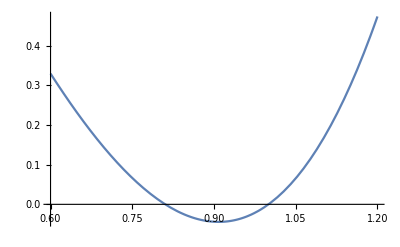

```mathematica
f[x_]:=x^4-3x+2;
Plot[f[x],{x,0.6,1.2}]
```

```mathematica
regulafalsi[0.7,0.9,20]
```

u = 0.852282608695652

f[u] = -0.02921172070130895

```mathematica
regulafalsi[0.9,1.1,15]
```

u = 0.972203721678961

f[u] = -0.02324578812561784

# Practical 3 Newton-Raphson Method

```mathematica
ClearAll;
```

```mathematica
newtonraphson[f_,a0_,n_]:=Module[{},aold=N[a0];
df[x_]=D[f[x],x];
i=1;
While[i<=n,anew=N[aold-N[f[aold]]/N[df[aold]]];
Print[i,"            ",anew];
i++;
aold=anew;] Print["Root = ",anew];]
```

#### Question 1

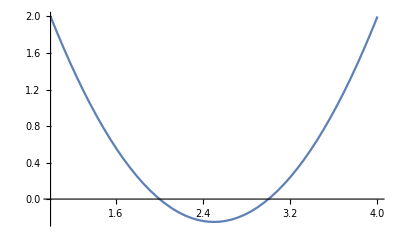

```mathematica
f[x_]:=x^2-5x+6;
Plot[f[x],{x,1,4}]
```

```mathematica
newtonraphson[f,1.8,5]
```

1            1.97143

2            1.99923

3            2.

4            2.

5            2.

Root = 2.

```mathematica
newtonraphson[f,10,8]
```

1            6.26667

2            4.41652

3            3.52348

4            3.13387

5            3.01414

6            3.00019

7            3.

8            3.

Root = 3.

#### Question 2

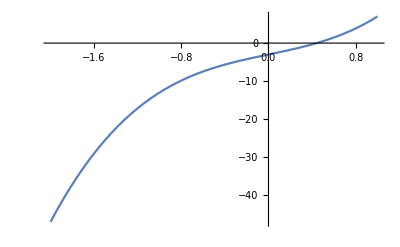

```mathematica
f[x_]:=4x^3+6x-3;
Plot[f[x],{x,-2,1}]
```

```mathematica
newtonraphson[f,-2,7]
```

1            -1.12963

2            -0.400316

3            0.313868

4            0.452143

5            0.442373

6            0.442311

7            0.442311

Root = 0.442311

#### Question 3

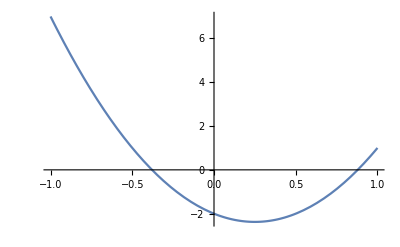

```mathematica
f[x_]:=6x^2-3x-2;
Plot[f[x],{x,-1,1}]
```

```mathematica
newtonraphson[f,-2,7]
```

1            -0.962963

2            -0.519649

3            -0.391976

4            -0.379281

5            -0.379153

6            -0.379153

7            -0.379153

Root = -0.379153

```mathematica
newtonraphson[f,3,10]
```

1            1.69697

2            1.11026

3            0.910197

4            0.879883

5            0.879153

6            0.879153

7            0.879153

8            0.879153

9            0.879153

10            0.879153

Root = 0.879153

#### Question 4

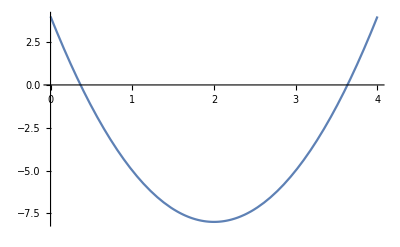

```mathematica
f[x_]:=3x^2-12x+4;
Plot[f[x],{x,0,4}]
```

```mathematica
newtonraphson[f,-1,10]
```

1            0.0555556

2            0.342063

3            0.366819

4            0.367007

5            0.367007

6            0.367007

7            0.367007

8            0.367007

9            0.367007

10            0.367007

Root = 0.367007

```mathematica
newtonraphson[f,5,10]
```

1            3.94444

2            3.65794

3            3.63318

4            3.63299

5            3.63299

6            3.63299

7            3.63299

8            3.63299

9            3.63299

10            3.63299

Root = 3.63299

# Practical 4 Gaussian Elimination

```mathematica
ClearAll;
```

#### Question 1 2 x_1-3 x_2+10 x_3=-2 x_1 - 2 x_2+ 3 x_3= -2 -x_1 + 3 x_2+ x_3= 4

```mathematica
m = ({{2, -3, 10}, {1, -2, 3}, {-1, 3, 1}});
x = ({{x1}, {x2}, {x3}});
b = ({{-2}, {-2}, {4}});
m.x==b
```

{{2 x1-3 x2+10 x3},{x1-2 x2+3 x3},{-x1+3 x2+x3}}=={{-2},{-2},{4}}

```mathematica
ArrayFlatten[{{m,b}}] //MatrixForm
```

(2 | -3 | 10 | -2
1 | -2 | 3 | -2
-1 | 3 | 1 | 4)

```mathematica
k= LinearSolve[m,b]
```

{{2},{2},{0}}

```mathematica
Flatten[k]
```

{2,2,0}

#### Question 2 x_1+2 x_2-3 x_3=-4 3 x_1- x_2+ 2 x_3= 3 -x_1 + 2 x_2- 5 x_3= -7

```mathematica
m = ({{1, 2, -3}, {3, -1, 2}, {-1, 2, -5}});
x = ({{x1}, {x2}, {x3}});
b = ({{-4}, {3}, {-7}});
m.x==b
```

{{x1+2 x2-3 x3},{3 x1-x2+2 x3},{-x1+2 x2-5 x3}}=={{-4},{3},{-7}}

```mathematica
ArrayFlatten[{{m,b}}] //MatrixForm
```

(1 | 2 | -3 | -4
3 | -1 | 2 | 3
-1 | 2 | -5 | -7)

```mathematica
k= LinearSolve[m,b]
```

{{1/12},{1/12},{17/12}}

```mathematica
Flatten[k]
```

{1/12,1/12,17/12}

#### Question 3 3x_1+x_2-6 x_3=-5 x_1+2 x_2 - 4 x_3= 12 3 x_1 + x_2- 2 x_3= -3

```mathematica
m = ({{3, 1, -6}, {1, 2, -4}, {3, 1, -2}});
x = ({{x1}, {x2}, {x3}});
b = ({{-5}, {12}, {-3}});
m.x==b
```

{{3 x1+x2-6 x3},{x1+2 x2-4 x3},{3 x1+x2-2 x3}}=={{-5},{12},{-3}}

```mathematica
ArrayFlatten[{{m,b}}] //MatrixForm
```

(3 | 1 | -6 | -5
1 | 2 | -4 | 12
3 | 1 | -2 | -3)

```mathematica
k= LinearSolve[m,b]
```

{{-18/5},{44/5},{1/2}}

```mathematica
Flatten[k]
```

{-18/5,44/5,1/2}

#### Question 4 4x_1-2 x_2+x_3=4 3x_1+7 x_2 - 3 x_3= -6 x_1 -5 x_2- 2 x_3= 5

```mathematica
m = ({{4, -2, 1}, {3, 7, -3}, {1, -5, -2}});
x = ({{x1}, {x2}, {x3}});
b = ({{4}, {-6}, {5}});
m.x==b
```

{{4 x1-2 x2+x3},{3 x1+7 x2-3 x3},{x1-5 x2-2 x3}}=={{4},{-6},{5}}

```mathematica
ArrayFlatten[{{m,b}}] //MatrixForm
```

(4 | -2 | 1 | 4
3 | 7 | -3 | -6
1 | -5 | -2 | 5)

```mathematica
k= LinearSolve[m,b]
```

{{67/144},{-47/48},{13/72}}

```mathematica
Flatten[k]
```

{67/144,-47/48,13/72}

# Gauss-Jordan Method

```mathematica
ClearAll;
```

#### Question 1 x_1+4 x_2+x_3=12 4 x_1 + 2 x_2- x_3= -5 -x_1 + 7 x_2- 2 x_3= -4

```mathematica
m = ({{1, 4, 1}, {4, 2, -1}, {-1, 7, -2}});
x = ({{x1}, {x2}, {x3}});
b = ({{12}, {-5}, {-4}});
m.x==b
```

{{x1+4 x2+x3},{4 x1+2 x2-x3},{-x1+7 x2-2 x3}}=={{12},{-5},{-4}}

```mathematica
ArrayFlatten[{{m,b}}] //MatrixForm
```

(1 | 4 | 1 | 12
4 | 2 | -1 | -5
-1 | 7 | -2 | -4)

```mathematica
RowReduce[%]//MatrixForm
```

(1 | 0 | 0 | -5/23
0 | 1 | 0 | 31/23
0 | 0 | 1 | 157/23)

```mathematica
k=LinearSolve[m,b]
```

{{-5/23},{31/23},{157/23}}

```mathematica
Flatten[k]
```

{-5/23,31/23,157/23}

#### Question 2 6 x_1+x_2-3 x_3=-1 x_1 + 3 x_2-2 x_3= 6 -2 x_1 + x_2+ 8 x_3= -7

```mathematica
m = ({{6, 1, -3}, {1, 3, -2}, {-2, 1, 8}});
x = ({{x1}, {x2}, {x3}});
b = ({{-1}, {6}, {-7}});
m.x==b
```

{{6 x1+x2-3 x3},{x1+3 x2-2 x3},{-2 x1+x2+8 x3}}=={{-1},{6},{-7}}

```mathematica
ArrayFlatten[{{m,b}}] //MatrixForm
```

(6 | 1 | -3 | -1
1 | 3 | -2 | 6
-2 | 1 | 8 | -7)

```mathematica
RowReduce[%]//MatrixForm
```

(1 | 0 | 0 | -141/131
0 | 1 | 0 | 193/131
0 | 0 | 1 | -174/131)

```mathematica
k=LinearSolve[m,b]
```

{{-141/131},{193/131},{-174/131}}

```mathematica
Flatten[k]
```

{-141/131,193/131,-174/131}

#### Question 3 x_1+12 x_2-x_3=11 4 x_1 + x_2-7x_3= 9 -x_1 + 2 x_2-9 x_3= -18

```mathematica
m = ({{1, 12, -1}, {4, 1, -7}, {-1, 2, -9}});
x = ({{x1}, {x2}, {x3}});
b = ({{11}, {9}, {-18}});
m.x==b
```

{{x1+12 x2-x3},{4 x1+x2-7 x3},{-x1+2 x2-9 x3}}=={{11},{9},{-18}}

```mathematica
ArrayFlatten[{{m,b}}] //MatrixForm
```

(1 | 12 | -1 | 11
4 | 1 | -7 | 9
-1 | 2 | -9 | -18)

```mathematica
RowReduce[%]//MatrixForm
```

(1 | 0 | 0 | 2503/512
0 | 1 | 0 | 329/512
0 | 0 | 1 | 819/512)

```mathematica
k=LinearSolve[m,b]
```

{{2503/512},{329/512},{819/512}}

```mathematica
Flatten[k]
```

{2503/512,329/512,819/512}

#### Question 4 2 x_1+x_2+x_3=10 3 x_1 + 2 x_2-3x_3= 9 x_1 + 4 x_2+9 x_3= 16

```mathematica
m = ({{2, 1, 1}, {3, 2, -3}, {1, 4, 9}});
x = ({{x1}, {x2}, {x3}});
b = ({{10}, {9}, {16}});
m.x==b
```

{{2 x1+x2+x3},{3 x1+2 x2-3 x3},{x1+4 x2+9 x3}}=={{10},{9},{16}}

```mathematica
ArrayFlatten[{{m,b}}] //MatrixForm
```

(2 | 1 | 1 | 10
3 | 2 | -3 | 9
1 | 4 | 9 | 16)

```mathematica
RowReduce[%]//MatrixForm
```

(1 | 0 | 0 | 35/8
0 | 1 | 0 | -3/40
0 | 0 | 1 | 53/40)

```mathematica
k=LinearSolve[m,b]
```

{{35/8},{-3/40},{53/40}}

```mathematica
Flatten[k]
```

{35/8,-3/40,53/40}

# Practical 5 Jacobi Method

```mathematica
ClearAll;
```

```mathematica
jacobi[a0_, b0_, p0_, max_] := Module[{a = N[a0], b = N[b0],
i, j, k = 0, n = Length[p0], p = p0, pOld = p0}, Print[Subscript["P", 0], "=", p];
While[ k < max,
For[i = 1, i<=n, i++,
p[[i]] = 1/a[[i, i]](b[[i]] + a[[i,i]] pOld[[i]] - ∑_(j=1)^n a[[i, j]]pOld[[j]])];
Print[Subscript["P", k+1], "=", p];
pOld=p;
k = k+1;];
Return[p];];
```

### Question 1 x_1 + 4 x_2 - 2 x_3 = 6 -3x_1 + 2x_2 + x_3 = 5 6x_1 + x_2 -7x_3 = -3

```mathematica
a = ({{1, 4, -2}, {-3, 2, 1}, {6, 1, -7}});
b = {6, 5, -3};
vars = {"x1", "x2", "x3"};
Print["Solve the System"];
Print[MatrixForm[a], MatrixForm[vars], "=", MatrixForm[b]];
```

Solve the System

(1 | 4 | -2
-3 | 2 | 1
6 | 1 | -7)(x1
x2
x3)=(6
5
-3)

```mathematica
p = {0, 0 , 0};
x = jacobi[a, b, p, 4];
```

P_0={0,0,0}

P_1={6.,2.5,0.428571}

P_2={-3.14286,11.2857,5.92857}

P_3={-27.2857,-5.17857,-0.653061}

P_4={25.4082,-38.102,-23.699}

### Question 2 6x_1 + 2 x_2 + x_3 = 4 x_1 - 2x_2 + 6 x_3 = -12 7x_1 + 3x_2 + 2 x_3 = 8

```mathematica
a = ({{6, 2, 1}, {1, -2, 6}, {7, 3, 2}});
b = {4, -12, 8};
vars = {"x1", "x2", "x3"};
Print["Solve the System"];
Print[MatrixForm[a], MatrixForm[vars], "=", MatrixForm[b]];
```

Solve the System

(6 | 2 | 1
1 | -2 | 6
7 | 3 | 2)(x1
x2
x3)=(4
-12
8)

```mathematica
p = {0, 0 , 0};
x = jacobi[a, b, p, 4];
```

P_0={0,0,0}

P_1={0.666667,6.,4.}

P_2={-2.,18.3333,-7.33333}

P_3={-4.22222,-17.,-16.5}

P_4={9.08333,-45.6111,44.2778}

### Question 3 x_1 + 4 x_2 + x_3 = 6 6 x_1 + 4x_2 + 3 x_3 = 18 2x_1 - x_2 + 2 x_3 = -6

```mathematica
a = ({{1, 4, 1}, {6, 4, 3}, {2, -1, 2}});
b = {6, 18, -6};
vars = {"x1", "x2", "x3"};
Print["Solve the System"];
Print[MatrixForm[a], MatrixForm[vars], "=", MatrixForm[b]];
```

Solve the System

(1 | 4 | 1
6 | 4 | 3
2 | -1 | 2)(x1
x2
x3)=(6
18
-6)

```mathematica
p = {0, 0 , 0};
x = jacobi[a, b, p, 4];
```

P_0={0,0,0}

P_1={6.,4.5,-3.}

P_2={-9.,-2.25,-6.75}

P_3={21.75,23.0625,4.875}

P_4={-91.125,-31.7813,-13.2188}

### Question 4 5 x_1 + 4 x_2 + x_3 = 6 16 x_1 + x_2 + 3 x_3 = 8 7x_1 - 10x_2 + 2 x_3 = 5

```mathematica
a = ({{5, 4, 1}, {16, 1, 3}, {7, -10, 2}});
b = {6, 8, 5};
vars = {"x1", "x2", "x3"};
Print["Solve the System"];
Print[MatrixForm[a], MatrixForm[vars], "=", MatrixForm[b]];
```

Solve the System

(5 | 4 | 1
16 | 1 | 3
7 | -10 | 2)(x1
x2
x3)=(6
8
5)

```mathematica
p = {0, 0 , 0};
x = jacobi[a, b, p, 4];
```

P_0={0,0,0}

P_1={1.2,8.,2.5}

P_2={-5.7,-18.7,38.3}

P_3={8.5,-15.7,-71.05}

P_4={27.97,85.15,-105.75}

# Gauss-Seidel Method

```mathematica
ClearAll;
```

```mathematica
gaussseidel[a0_, b0_, p0_, max_] := Module[{a = N[a0], b = N[b0],
i, j, k = 0, n = Length[p0], p = p0}, Print[Subscript["P", 0], "=", p];
While[k < max,
For[i = 1,  i <=n, i++,
p[[i]] = 1/a[[i, i]](b[[i]] + a[[i, i]] p[[i]] - ∑_(j=1)^n a[[i, j]] p[[j]])];
Print[Subscript["P", k+1], "=", p];
k = k+1;];
Return[p];];
```

### Question 1 x_1 + 4 x_2 + x_3 = 6 6 x_1 + 4x_2 + 3 x_3 = 18 2x_1 - x_2 + 2 x_3 = -6

```mathematica
a = ({{1, 4, 1}, {6, 4, 3}, {2, -1, 2}});
b = {6,18, -6};
vars = {"x1", "x2", "x3"};
Print["Solve the System"];
Print[MatrixForm[a], MatrixForm[vars], "=", MatrixForm[b]];
```

Solve the System

(1 | 4 | 1
6 | 4 | 3
2 | -1 | 2)(x1
x2
x3)=(6
18
-6)

```mathematica
p= {0, 1, 1};
x = gaussseidel[a, b, p, 10];
Print["a x = ", MatrixForm[a.x], " = ", MatrixForm[b], "= b"];
```

P_0={0,1,1}

P_1={1.,2.25,-2.875}

P_2={-0.125,6.84375,0.546875}

P_3={-21.9219,36.9727,37.4082}

P_4={-179.299,245.392,298.995}

P_5={-1274.56,1692.1,2117.61}

P_6={-8880.01,11736.3,14745.2}

P_7={-61684.4,81472.2,102417.}

P_8={-428300.,565642.,711118.}

P_9={-2.97368×10^6,3.92718×10^6,4.93727×10^6}

P_10={-2.0646×10^7,2.7266×10^7,3.4279×10^7}

a x = (1.22697×10^8
8.80253×10^7
-6.) = (6
18
-6)= b

### Question 2 5 x_1 + 4 x_2 + x_3 = 6 16 x_1 + x_2 + 3 x_3 = 8 7x_1 - 10x_2 + 2 x_3 = 5

```mathematica
a = ({{5, 4, 1}, {16, 1, 3}, {7, -10, 2}});
b = {6, 8, 5};
vars = {"x1", "x2", "x3"};
Print["Solve the System"];
Print[MatrixForm[a], MatrixForm[vars], "=", MatrixForm[b]];
```

Solve the System

(5 | 4 | 1
16 | 1 | 3
7 | -10 | 2)(x1
x2
x3)=(6
8
5)

```mathematica
p= {0, 1, 1};
x = gaussseidel[a, b, p, 10];
Print["a x = ", MatrixForm[a.x], " = ", MatrixForm[b], "= b"];
```

P_0={0,1,1}

P_1={0.2,1.8,10.8}

P_2={-2.4,14.,80.9}

P_3={-26.18,184.18,1015.03}

P_4={-349.15,2549.31,13971.1}

P_5={-4832.46,35414.2,193987.}

P_6={-67127.6,492088.,2.69539×10^6}

P_7={-932747.,6.83779×10^6,3.74536×10^7}

P_8={-1.29609×10^7,9.50144×10^7,5.20435×10^8}

P_9={-1.80099×10^8,1.32027×10^9,7.2317×10^9}

P_10={-2.50256×10^9,1.83458×10^10,1.00488×10^11}

a x = (1.61359×10^11
2.79769×10^11
5.) = (6
8
5)= b

### Question 3 x_1 + 4 x_2 - 2 x_3 = 6 -3x_1 + 2x_2 + x_3 = 5 6x_1 + x_2 -7x_3 = -3

```mathematica
a = ({{1, 4, -2}, {-3, 2, 1}, {6, 1, -7}});
b = {6, 5, -3};
vars = {"x1", "x2", "x3"};
Print["Solve the System"];
Print[MatrixForm[a], MatrixForm[vars], "=", MatrixForm[b]];
```

Solve the System

(1 | 4 | -2
-3 | 2 | 1
6 | 1 | -7)(x1
x2
x3)=(6
5
-3)

```mathematica
p= {0, 1, 1};
x = gaussseidel[a, b, p, 10];
Print["a x = ", MatrixForm[a.x], " = ", MatrixForm[b], "= b"];
```

P_0={0,1,1}

P_1={4.,8.,5.}

P_2={-16.,-24.,-16.7143}

P_3={68.5714,113.714,75.449}

P_4={-297.959,-482.163,-323.845}

P_5={1286.96,2094.87,1402.81}

P_6={-5567.85,-9050.68,-6064.97}

P_7={24078.8,39153.2,26232.7}

P_8={-104141.,-169326.,-113453.}

P_9={450403.,732334.,490679.}

P_10={-1.94797×10^6,-3.16729×10^6,-2.12216×10^6}

a x = (-1.03728×10^7
-2.61283×10^6
-3.) = (6
5
-3)= b

### Question 4 6x_1 + 2 x_2 + x_3 = 4 x_1 - 2x_2 + 6 x_3 = -12 7x_1 + 3x_2 + 2 x_3 = 8

```mathematica
a = ({{6, 2, 1}, {1, -2, 6}, {7, 3, 2}});
b = {4, -12, 8};
vars = {"x1", "x2", "x3"};
Print["Solve the System"];
Print[MatrixForm[a], MatrixForm[vars], "=", MatrixForm[b]];
```

Solve the System

(6 | 2 | 1
1 | -2 | 6
7 | 3 | 2)(x1
x2
x3)=(4
-12
8)

```mathematica
p= {0, 1, 1};
x = gaussseidel[a, b, p, 10];
Print["a x = ", MatrixForm[a.x], " = ", MatrixForm[b], "= b"];
```

P_0={0,1,1}

P_1={0.166667,9.08333,-10.2083}

P_2={-0.659722,-24.9549,43.7413}

P_3={1.69473,138.071,-209.039}

P_4={-10.5173,-626.374,980.372}

P_5={46.0627,2970.15,-4612.44}

P_6={-220.642,-13941.6,21688.7}

P_7={1033.1,65588.7,-101995.}

P_8={-4863.09,-308410.,479640.}

P_9={22864.1,1.45036×10^6,-2.25556×10^6}

P_10={-107526.,-6.82043×10^6,1.0607×10^7}

a x = (-3.67903×10^6
7.71753×10^7
8.) = (4
-12
8)= b

# Practical 6 Lagrange Interpolation

```mathematica
ClearAll;
```

#### Question 1

```mathematica
sum = 0;
points = {{1, 2}, {3, 5}, {8, 11}};
no = Length[points]
y = points[[All, 1]]
f = points[[All, 2]]
lagrange[no_, n_] :=
Product[If[Equal[k,n ], 1, (x - y[[k]])/(y[[n]]-y[[k]])], {k,1, no}]
For[i=1, i<=no, i++,sum+= (f[[i]]*lagrange[no, i])]
Expand[sum]
sum/.x->2.5
```

3

{1,3,8}

{2,5,11}

13/35+(117 x)/70-(3 x^2)/70

4.28214

#### Question 2

```mathematica
sum = 0;
points = {{2, 3}, {11, 14}, {16, 18}};
no = Length[points]
y = points[[All, 1]]
f = points[[All, 2]]
lagrange[no_, n_] :=
Product[If[Equal[k,n ], 1, (x - y[[k]])/(y[[n]]-y[[k]])], {k,1, no}]
For[i=1, i<=no, i++,sum+= (f[[i]]*lagrange[no, i])]
Expand[sum]
sum/.x->2.5
```

3

{2,11,16}

{3,14,18}

-34/315+(113 x)/70-(19 x^2)/630

3.73929

#### Question 3

```mathematica
sum = 0;
points = {{2, 4}, {6, 8}, {10, 12}};
no = Length[points]
y = points[[All, 1]]
f = points[[All, 2]]
lagrange[no_, n_] :=
Product[If[Equal[k,n ], 1, (x - y[[k]])/(y[[n]]-y[[k]])], {k,1, no}]
For[i=1, i<=no, i++,sum+= (f[[i]]*lagrange[no, i])]
Expand[sum]
sum/.x->2.5
```

3

{2,6,10}

{4,8,12}

2+x

4.5

#### Question 4

```mathematica
sum = 0;
points = {{4, 5}, {6, 9}, {11, 13}};
no = Length[points]
y = points[[All, 1]]
f = points[[All, 2]]
lagrange[no_, n_] :=
Product[If[Equal[k,n ], 1, (x - y[[k]])/(y[[n]]-y[[k]])], {k,1, no}]
For[i=1, i<=no, i++,sum+= (f[[i]]*lagrange[no, i])]
Expand[sum]
sum/.x->2.5
```

3

{4,6,11}

{5,9,13}

-249/35+(26 x)/7-(6 x^2)/35

1.1

# Newton Interpolation

```mathematica
ClearAll;
Clear[x];
Clear[p];
```

#### Question 1

```mathematica
sum = 0;
points = {{3, 420}, {5, 576}, {6, 690}, {9, 786}};
n = Length[points];
y = points[[All, 1]];
f = points[[All, 2]];
dd[k_] :=
Sum[(f[[i]]/Product[If[Equal[j, i], 1, (y[[i]]-y[[j]])], {j, 1, k}]), {i, 1, k}]
p[x_] = Sum[(dd[i] * Product[If[i<=j, 1, x-y[[j]]],{j, 1, i-1}]), {i, 1, n}]
Simplify[p[x]]
Evaluate[p[2.5]]
```

420+78 (-3+x)+12 (-5+x) (-3+x)-65/12 (-6+x) (-5+x) (-3+x)

1/12 (10242-4311 x+1054 x^2-65 x^3)

419.698

#### Question 2

```mathematica
sum = 0;
points = {{1, 211}, {2, 310}, {6, 507}, {9, 612}};
n = Length[points];
y = points[[All, 1]];
f = points[[All, 2]];
dd[k_] :=
Sum[(f[[i]]/Product[If[Equal[j, i], 1, (y[[i]]-y[[j]])], {j, 1, k}]), {i, 1, k}]
p[x_] = Sum[(dd[i] * Product[If[i<=j, 1, x-y[[j]]],{j, 1, i-1}]), {i, 1, n}]
Simplify[p[x]]
Evaluate[p[2.5]]
```

211+99 (-1+x)-199/20 (-2+x) (-1+x)+277/280 (-6+x) (-2+x) (-1+x)

1/280 (22464+41618 x-5279 x^2+277 x^3)

349.441

#### Question 3

```mathematica
sum = 0;
points = {{2, 111}, {5, 322}, {6, 530}, {7, 911}};
n = Length[points];
y = points[[All, 1]];
f = points[[All, 2]];
dd[k_] :=
Sum[(f[[i]]/Product[If[Equal[j, i], 1, (y[[i]]-y[[j]])], {j, 1, k}]), {i, 1, k}]
p[x_] = Sum[(dd[i] * Product[If[i<=j, 1, x-y[[j]]],{j, 1, i-1}]), {i, 1, n}]
Simplify[p[x]]
Evaluate[p[2.5]]
```

111+211/3 (-2+x)+413/12 (-5+x) (-2+x)+125/12 (-6+x) (-5+x) (-2+x)

1/12 (-3726+4453 x-1212 x^2+125 x^3)

148.719

#### Question 4

```mathematica
sum = 0;
points = {{0, 76}, {3, 222}, {7, 368}, {8, 560}};
n = Length[points];
y = points[[All, 1]];
f = points[[All, 2]];
dd[k_] :=
Sum[(f[[i]]/Product[If[Equal[j, i], 1, (y[[i]]-y[[j]])], {j, 1, k}]), {i, 1, k}]
p[x_] = Sum[(dd[i] * Product[If[i<=j, 1, x-y[[j]]],{j, 1, i-1}]), {i, 1, n}]
Simplify[p[x]]
Evaluate[p[2.5]]
```

76+(146 x)/3-73/42 (-3+x) x+431/105 (-7+x) (-3+x) x

1/210 (15960+29417 x-8985 x^2+862 x^3)

222.929

# Practical 7 Trapezoidal Rule

#### Question 1

```mathematica
TRAPEZOIDAL RULE:
TRAPEZOIDAL (RULE: Null);

ClearAll[n, x, f]

a = Input["Enter the left end point: "]
b = Input["Enter the right end point: "]
n = Input["Enter the number of sub intervals to be formed: "]
sum = 0;
h = (b-a)/n
f[x] = Cos[x] - x * Exp[x]
For[i=1, i≤n-1, i++, sum += N[f[x]/. x -> (a+i*h)]]
sum = N[(2*sum+f[x]/.x-> a+f[x]/.x->b)*h/2]
```

-1

1

10

1/5

-ⅇ^x x+Cos[x]

0.963759

#### Question 2

```mathematica
TRAPEZOIDAL RULE:
TRAPEZOIDAL (RULE: Null);

ClearAll[n, x, f]

a = Input["Enter the left end point: "]
b = Input["Enter the right end point: "]
n = Input["Enter the number of sub intervals to be formed: "]
sum = 0;
h = (b-a)/n
f[x] = x^2-x-1
For[i=1, i≤n-1, i++, sum += N[f[x]/. x -> (a+i*h)]]
sum = N[(2*sum+f[x]/.x-> a+f[x]/.x->b)*h/2]
```

-1

2

12

1/4

-1-x+x^2

-1.84375

#### Question 3

```mathematica
TRAPEZOIDAL RULE:
TRAPEZOIDAL (RULE: Null);

ClearAll[n, x, f]

a = Input["Enter the left end point: "]
b = Input["Enter the right end point: "]
n = Input["Enter the number of sub intervals to be formed: "]
sum = 0;
h = (b-a)/n
f[x] =2x^3+4x-3
For[i=1, i≤n-1, i++, sum += N[f[x]/. x -> (a+i*h)]]
sum = N[(2*sum+f[x]/.x-> a+f[x]/.x->b)*h/2]
```

0

1

10

1/10

-3+4 x+2 x^3

2.655

#### Question 4

```mathematica
TRAPEZOIDAL RULE:
TRAPEZOIDAL (RULE: Null);

ClearAll[n, x, f]

a = Input["Enter the left end point: "]
b = Input["Enter the right end point: "]
n = Input["Enter the number of sub intervals to be formed: "]
sum = 0;
h = (b-a)/n
f[x] =6x^2-3x-2
For[i=1, i≤n-1, i++, sum += N[f[x]/. x -> (a+i*h)]]
sum = N[(2*sum+f[x]/.x-> a+f[x]/.x->b)*h/2]
```

-1

1

14

1/7

-2-3 x+6 x^2

-0.673469

# Simpson’s Rule

```mathematica
ClearAll;
```

#### Question 1

```mathematica
a = Input["Enter the left end point: "]
b = Input["Enter the right end point: "]
n = Input["Enter the number of sub intervals to be formed: "]
h = (b-a)/n;
y = Table[a + i h, {i, 1, n}];
f[x] := x^4-3x+2
sumodd = 0;
sumeven = 0;
For[i=1, i <n, i += 2, sumodd+=4*f[x]/.x->y[[i]]];
For[i=2, i <n, i += 2, sumeven+=2*f[x]/.x->y[[i]]];
Sn = (h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b));
Print["For n = ", n, ", Simpson Estimate is: ", Sn]
in = Integrate[f[x], {x, 1, 2}];
Print["True Value is ", in]
Print["Absoulte Errors is ", Abs[Sn-in]]
```

0

2

15

For n = 15, Simpson Estimate is: 3.95247

True Value is 37/10

Absoulte Errors is 0.252466

#### Question 2

```mathematica
a = Input["Enter the left end point: "]
b = Input["Enter the right end point: "]
n = Input["Enter the number of sub intervals to be formed: "]
h = (b-a)/n;
y = Table[a + i h, {i, 1, n}];
f[x] := x^2-x-1
sumodd = 0;
sumeven = 0;
For[i=1, i <n, i += 2, sumodd+=4*f[x]/.x->y[[i]]];
For[i=2, i <n, i += 2, sumeven+=2*f[x]/.x->y[[i]]];
Sn = (h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b));
Print["For n = ", n, ", Simpson Estimate is: ", Sn]
in = Integrate[f[x], {x, 1, 2}];
Print["True Value is ", in]
Print["Absoulte Errors is ", Abs[Sn-in]]
```

-2

2

16

For n = 16, Simpson Estimate is: 1.33333

True Value is -1/6

Absoulte Errors is 1.5

#### Question 3

```mathematica
a = Input["Enter the left end point: "]
b = Input["Enter the right end point: "]
n = Input["Enter the number of sub intervals to be formed: "]
h = (b-a)/n;
y = Table[a + i h, {i, 1, n}];
f[x] := -Sin[x]
sumodd = 0;
sumeven = 0;
For[i=1, i <n, i += 2, sumodd+=4*f[x]/.x->y[[i]]];
For[i=2, i <n, i += 2, sumeven+=2*f[x]/.x->y[[i]]];
Sn = (h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b));
Print["For n = ", n, ", Simpson Estimate is: ", Sn]
in = Integrate[f[x], {x, 1, 2}];
Print["True Value is ", in]
Print["Absoulte Errors is ", Abs[Sn-in]]
```

-1

3

14

For n = 14, Simpson Estimate is: -1.53035

True Value is -Cos[1]+Cos[2]

Absoulte Errors is 0.573903

#### Question 4

```mathematica
a = Input["Enter the left end point: "]
b = Input["Enter the right end point: "]
n = Input["Enter the number of sub intervals to be formed: "]
h = (b-a)/n;
y = Table[a + i h, {i, 1, n}];
f[x] := 1/(2x) + Cos[x]
sumodd = 0;
sumeven = 0;
For[i=1, i <n, i += 2, sumodd+=4*f[x]/.x->y[[i]]];
For[i=2, i <n, i += 2, sumeven+=2*f[x]/.x->y[[i]]];
Sn = (h/3)*((f[x]/.x->a)+N[sumodd]+N[sumeven]+(f[x]/.x->b));
Print["For n = ", n, ", Simpson Estimate is: ", Sn]
in = Integrate[f[x], {x, 1, 2}];
Print["True Value is ", in]
Print["Absoulte Errors is ", Abs[Sn-in]]
```

-1

1

15

For n = 15, Simpson Estimate is: 1.10914

True Value is Log[2]/2-Sin[1]+Sin[2]

Absoulte Errors is 0.694745

# Practical 8 Euler Methods for solving first order initial value problems of ODE’s.

```mathematica
ClearAll;
```

#### Question 1

```mathematica
Euler[x_, w_]:= w+h(4x^3-w)
h = 0.3; w=2
w=Euler[0, w]
w=Euler[0.3, w]
w=Euler[0.6, w]
w=Euler[0.9, w]
w=Euler[0.12, w]
w=Euler[0.15, w]
w=Euler[0.18, w]
w=Euler[0.21, w]
w=Euler[0.24, w]
w=Euler[0.27, w]
```

2

1.4

1.0124

0.96788

1.55232

1.08869

0.766136

0.543294

0.391419

0.290582

0.227027

#### Question 2

```mathematica
Euler[x_, w_]:= w+h( 5x^2-3w)
h = 0.1; w=4
w=Euler[0, w]
w=Euler[0.1, w]
w=Euler[0.2, w]
w=Euler[0.3, w]
w=Euler[0.4, w]
w=Euler[0.5, w]
w=Euler[0.6, w]
w=Euler[0.7, w]
w=Euler[0.8, w]
```

4

2.8

1.965

1.3955

1.02185

0.795295

0.681707

0.657195

0.705036

0.813525

#### Question 3

```mathematica
Euler[x_, w_]:= w+h(x^3+2x -w)
h = 0.2; w=2
w=Euler[0, w]
w=Euler[0.2, w]
w=Euler[0.4, w]
w=Euler[0.6, w]
w=Euler[0.8, w]
w=Euler[0.10, w]
w=Euler[0.12, w]
w=Euler[0.14, w]
```

2

1.6

1.3616

1.26208

1.29286

1.45669

1.20555

1.01279

0.866779

#### Question 4

```mathematica
Euler[x_, w_]:= w+h(5x - 2w)
h = 0.1; w=1
w=Euler[0, w]
w=Euler[0.1, w]
w=Euler[0.2, w]
w=Euler[0.3, w]
w=Euler[0.4, w]
w=Euler[0.5, w]
w=Euler[0.6, w]
```

1

0.8

0.69

0.652

0.6716

0.73728

0.839824

0.971859